## Струна

#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Explicit_eiler500.txt"]],Table[Real,n+1]];
T = {};
```

```mathematica
For[i=1,i≤500,i++,T = Append[T,{plots⟦i⟧⟦2⟧,plots⟦i⟧⟦3⟧}]]
```

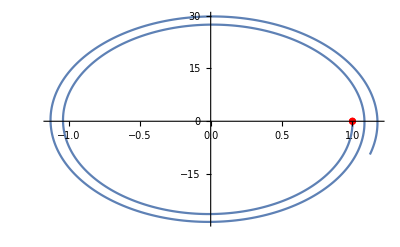

```mathematica
Show[ListLinePlot[T],ListPlot[{T⟦1⟧},PlotStyle->Red]]
```

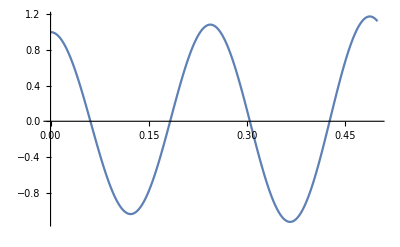

```mathematica
Realy={};
For[i=1,i≤500,i++,Realy = Append[Realy,{plots⟦i⟧⟦1⟧,plots⟦i⟧⟦2⟧}]]
ListLinePlot[Realy]
```

#### Неявный

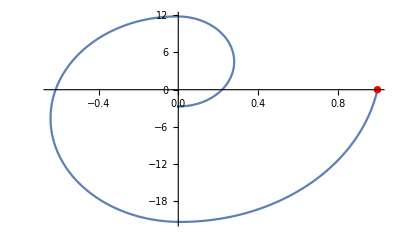

```mathematica
NotebookDirectory[];
n = 2;
plotsIm=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Implicit_eiler500.txt"]],Table[Real,n+1]];
TIm = {};
For[i=1,i≤500,i++,TIm = Append[TIm,{plotsIm⟦i⟧⟦2⟧,plotsIm⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TIm],ListPlot[{TIm⟦1⟧},PlotStyle->Red]]
```

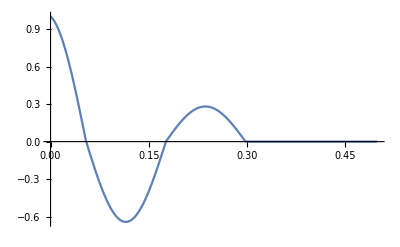

```mathematica
RealyIm={};
For[i=1,i≤500,i++,RealyIm = Append[RealyIm,{plotsIm⟦i⟧⟦1⟧,plotsIm⟦i⟧⟦2⟧}]]
ListLinePlot[RealyIm]
```

#### Симметричная схема

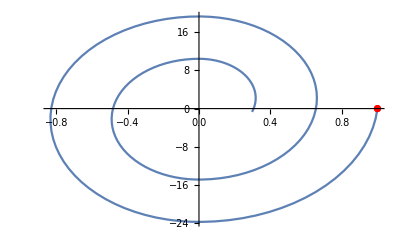

```mathematica
NotebookDirectory[];
n = 2;
plotsSym=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Sym_scheme.txt"]],Table[Real,n+1]];
TSym = {};
For[i=1,i≤Length[plotsSym],i++,TSym = Append[TSym,{plotsSym⟦i⟧⟦2⟧,plotsSym⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TSym],ListPlot[{TSym⟦1⟧},PlotStyle->Red]]
```

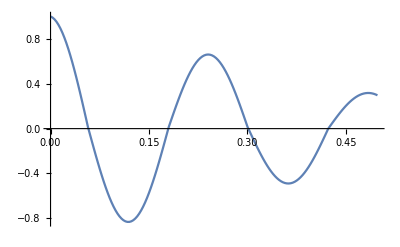

```mathematica
RealySym={};
For[i=1,i≤Length[plotsSym],i++,RealySym = Append[RealySym,{plotsSym⟦i⟧⟦1⟧,plotsSym⟦i⟧⟦2⟧}]]
ListLinePlot[RealySym]
```

#### Метод Адамса

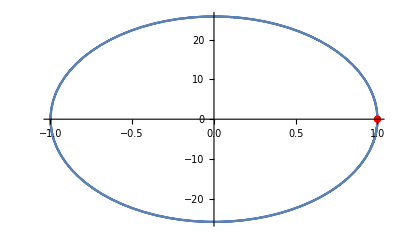

```mathematica
NotebookDirectory[];
n = 2;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Adams.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦2⟧,plotsAd⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TAd],ListPlot[{TAd⟦1⟧},PlotStyle->Red]]
```

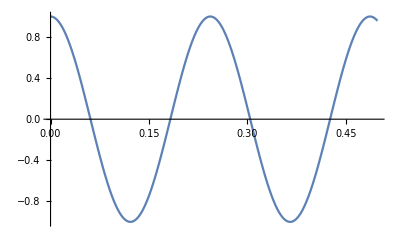

```mathematica
RealyAd={};
For[i=1,i≤Length[plotsAd],i++,RealyAd = Append[RealyAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦2⟧}]]
ListLinePlot[RealyAd]
```

#### Рунге - Кутты 2го порядка

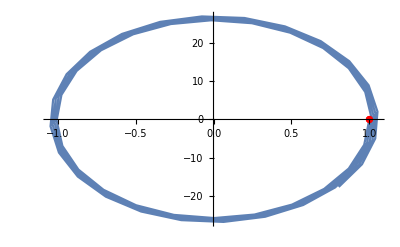

```mathematica
NotebookDirectory[];
n = 2;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_2_2.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦2⟧,plotsAd⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TAd],ListPlot[{TAd⟦1⟧},PlotStyle->Red]]
```

## Первый пример

#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Explicit_eiler.txt"]],Table[Real,n+1]];
T = {};
```

```mathematica
For[i=1,i≤Length[plots],i++,T = Append[T,{plots⟦i⟧⟦2⟧,plots⟦i⟧⟦3⟧}]]
```

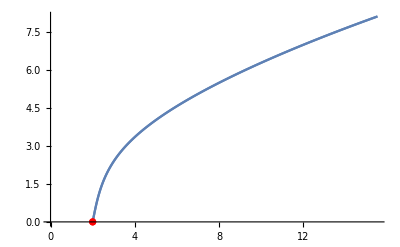

```mathematica
Show[ListLinePlot[T],ListPlot[{T⟦1⟧},PlotStyle->Red]]
```

#### Неявный

```mathematica
NotebookDirectory[];
n = 2;
plotsIm=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Implicit_eiler.txt"]],Table[Real,n+1]];
TIm = {};
For[i=1,i≤500,i++,TIm = Append[TIm,{plotsIm⟦i⟧⟦2⟧,plotsIm⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TIm],ListPlot[{TIm⟦1⟧},PlotStyle->Red]]
```

-Graphics-

#### Метод Адамса

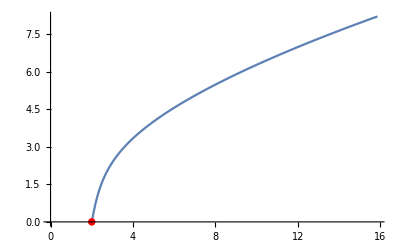

```mathematica
NotebookDirectory[];
n = 2;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Adams.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦2⟧,plotsAd⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TAd],ListPlot[{TAd⟦1⟧},PlotStyle->Red]]
```

## Второй пример

#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Explicit_eiler.txt"]],Table[Real,n+1]];
T = {};
```

```mathematica
For[i=1,i≤Length[plots],i++,T = Append[T,{plots⟦i⟧⟦2⟧,plots⟦i⟧⟦3⟧}]]
```

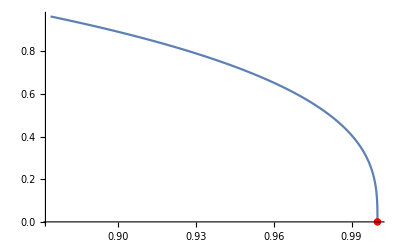

```mathematica
Show[ListLinePlot[T],ListPlot[{T⟦1⟧},PlotStyle->Red]]
```

#### Неявный

Part::partw: Part 2 of {{0.,2.,0.}} does not exist.

Part::partw: Part 3 of {{0.,2.,0.}}⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

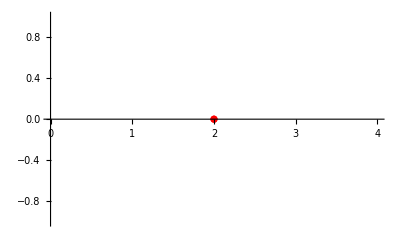

```mathematica
NotebookDirectory[];
n = 2;
plotsIm=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Implicit_eiler.txt"]],Table[Real,n+1]];
TIm = {};
For[i=1,i≤500,i++,TIm = Append[TIm,{plotsIm⟦i⟧⟦2⟧,plotsIm⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TIm],ListPlot[{TIm⟦1⟧},PlotStyle->Red]]
```

#### Метод Адамса

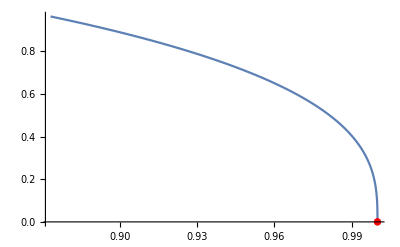

```mathematica
NotebookDirectory[];
n = 2;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Adams.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦2⟧,plotsAd⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TAd],ListPlot[{TAd⟦1⟧},PlotStyle->Red]]
```

## Третий пример

#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 3;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Explicit_eiler.txt"]],Table[Real,n+1]];
T = {};
```

```mathematica
For[i=1,i≤Length[plots],i++,T = Append[T,{plots⟦i⟧⟦2⟧,plots⟦i⟧⟦3⟧,plots⟦i⟧⟦4⟧}]]
```

```mathematica
Show[ListPlot3D[T](*,ListPlot3D[{T⟦1⟧},PlotStyle->Red]*)]
```

-Graphics3D-

#### Неявный

```mathematica
NotebookDirectory[];
n = 2;
plotsIm=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Implicit_eiler.txt"]],Table[Real,n+1]];
TIm = {};
For[i=1,i≤500,i++,TIm = Append[TIm,{plotsIm⟦i⟧⟦2⟧,plotsIm⟦i⟧⟦3⟧}]]
Show[ListLinePlot[TIm],ListPlot[{TIm⟦1⟧},PlotStyle->Red]]
```

Part::partw: Part 2 of {{0.,2.,0.}} does not exist.

Part::partw: Part 3 of {{0.,2.,0.}}⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

#### Метод Адамса

```mathematica
NotebookDirectory[];
n = 3;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Adams.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦2⟧,plotsAd⟦i⟧⟦3⟧, plotsAd⟦i⟧⟦4⟧}]]
Show[ListPlot3D[TAd](*,ListPlot[{TAd⟦1⟧},PlotStyle->Red]*)]
```

-Graphics3D-

## Первый пример фазовые траектории

#### Седло

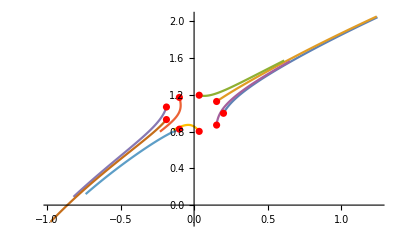

```mathematica
ClearAll["Global`*"];
n = 2;
k = 9;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤Length[plotsRK44],i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red]]
```

#### Фокус

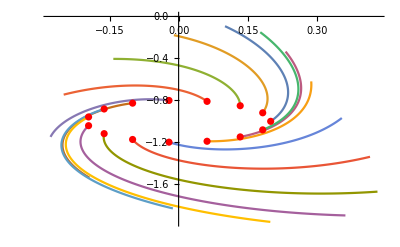

```mathematica
ClearAll["Global`*"];
n = 2;
k = 15;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤Length[plotsRK44],i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red]]
```

## Второй пример фазовые траектории

#### Центр

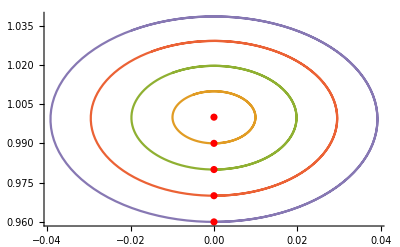

```mathematica
ClearAll["Global`*"];
n = 2;
k = 5;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤Length[plotsRK44],i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red]]
```

#### Седло

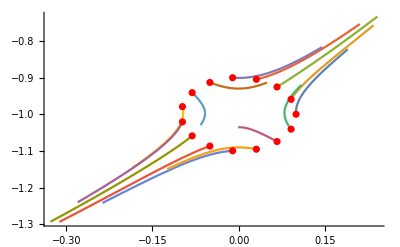

```mathematica
ClearAll["Global`*"];
n = 2;
k = 15;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤Length[plotsRK44],i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red]]
```

## Третий пример фазовые траектории

```mathematica
ClearAll["Global`*"];
```

```mathematica
NotebookDirectory[];
n = 3;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_0.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦2⟧,plotsAd⟦i⟧⟦3⟧, plotsAd⟦i⟧⟦4⟧}]]
Show[ListPointPlot3D[TAd],ListPointPlot3D[{TAd⟦1⟧},PlotStyle->Red]]
```

-Graphics3D-

## Наш пример фазовые траектории

#### Седло

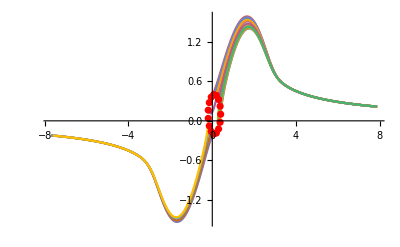

```mathematica
ClearAll["Global`*"];
n = 2;
k = 15;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤600,i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red]]
```

## Струна переменный шаг РК2

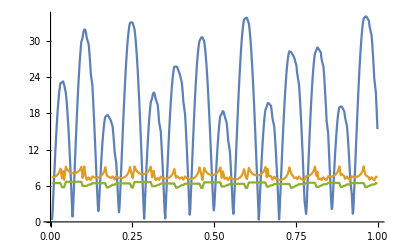

```mathematica
NotebookDirectory[];
n = 5;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_2_2_change.txt"]],Table[Real,n+1]];
NormAd={};
For[i=1,i≤Length[plotsAd],i++,NormAd = Append[NormAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦4⟧}]]
tauAd = {};
For[i=1,i≤Length[plotsAd],i++,tauAd = Append[tauAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦5⟧}]]
EpsAd = {};
For[i=1,i≤Length[plotsAd],i++,EpsAd = Append[EpsAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦6⟧}]]
eqAd = {};
For[i=1,i≤Length[plotsAd],i++,eqAd = Append[eqAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦1⟧}]]
ListLinePlot[{NormAd, EpsAd, tauAd}]
```

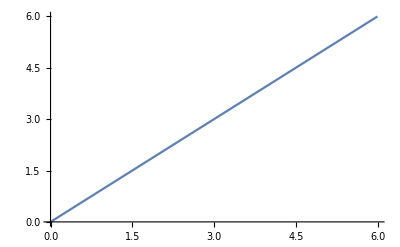

```mathematica
ListLinePlot[eqAd]
```

## Струна переменный шаг РК4

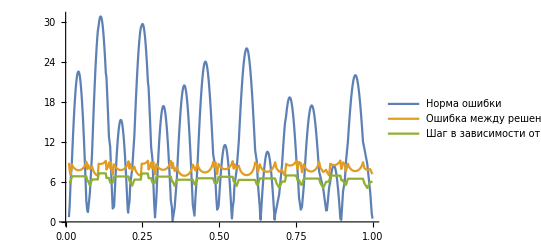

```mathematica
NotebookDirectory[];
ClearAll["Global`*"];
n = 5;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_change.txt"]],Table[Real,n+1]];
NormAd={};
For[i=1,i≤Length[plotsAd],i++,NormAd = Append[NormAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦4⟧}]]
tauAd = {};
For[i=1,i≤Length[plotsAd],i++,tauAd = Append[tauAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦5⟧}]]
EpsAd = {};
For[i=1,i≤Length[plotsAd],i++,EpsAd = Append[EpsAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦6⟧}]]
eqAd = {};
For[i=1,i≤Length[plotsAd],i++,eqAd = Append[eqAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦1⟧}]]
ListLinePlot[{NormAd, EpsAd, tauAd}, PlotLegends->{"Норма ошибки", "Ошибка между решениями", "Шаг в зависимости от времени"}]
```

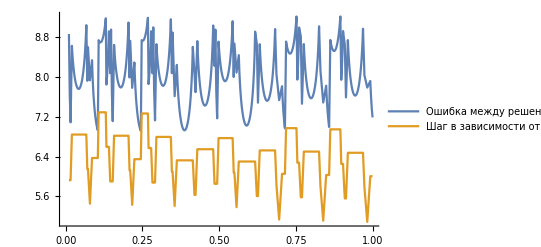

```mathematica
ListLinePlot[{EpsAd, tauAd}, PlotLegends->{"Ошибка между решениями", "Шаг в зависимости от времени"}]
```

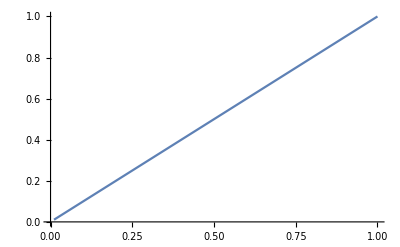

```mathematica
ListLinePlot[eqAd]
```

## Энергия

#### Рунге - Кутты 2го порядка

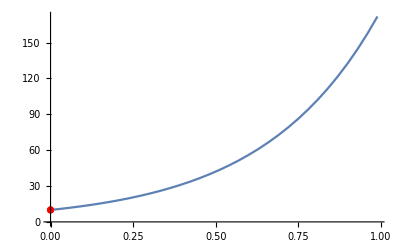

```mathematica
NotebookDirectory[];
n = 1;
plotsAd=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Energy.txt"]],Table[Real,n+1]];
TAd = {};
For[i=1,i≤Length[plotsAd],i++,TAd = Append[TAd,{plotsAd⟦i⟧⟦1⟧,plotsAd⟦i⟧⟦2⟧}]]
Show[ListLinePlot[TAd],ListPlot[{TAd⟦1⟧},PlotStyle->Red]]
```

## 2й вариант фазовые траектории

#### Фокус

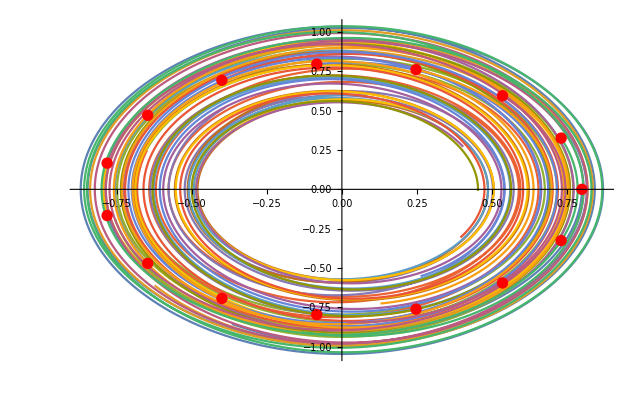

```mathematica
ClearAll["Global`*"];
n = 2;
k = 15;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤600,i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red]]
```

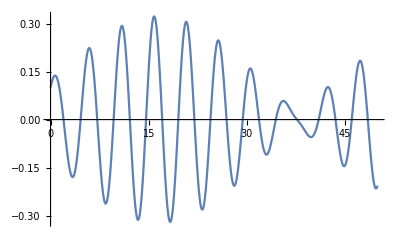

```mathematica
traektory=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_0.txt"]],Table[Real,n+1]];
Trk = {};
For[i=1,i≤Length[traektory],i++,Trk = Append[Trk,{traektory⟦i⟧⟦1⟧,traektory⟦i⟧⟦2⟧}]];
ListLinePlot[Trk]
```

## 6й вариант фазовые траектории

#### Фокус

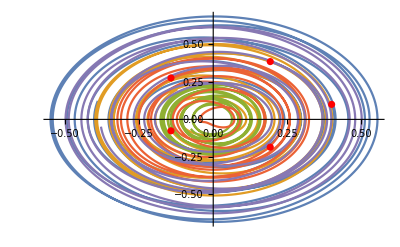

```mathematica
ClearAll["Global`*"];
n = 2;
k = 5;
PLOT = {};
For[j = 0, j < k, j++,
{plotsRK44=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_"<>ToString[j]<>".txt"]],Table[Real,n+1]];
TRK44 = {};
For[i=1,i≤Length[plotsRK44],i++,TRK44 = Append[TRK44,{plotsRK44⟦i⟧⟦2⟧,plotsRK44⟦i⟧⟦3⟧}]];
PLOT = Append[PLOT,TRK44]}]
Bplot = {};
i = 1;
For[i = 0, i < k, i++,
Bplot = Append[Bplot,PLOT⟦i+1⟧⟦1⟧]]
Show[ListLinePlot[PLOT],ListPlot[Bplot,PlotStyle->Red], PlotRange->All]
```

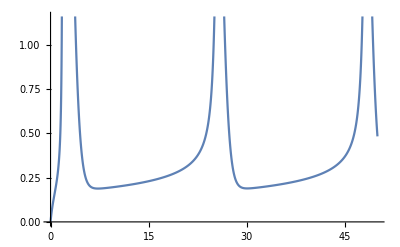

```mathematica
traektory=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Runge_Kut_4_4_0.txt"]],Table[Real,n+1]];
Trk = {};
For[i=1,i≤Length[traektory],i++,Trk = Append[Trk,{traektory⟦i⟧⟦1⟧,traektory⟦i⟧⟦2⟧}]];
ListLinePlot[Trk]
```

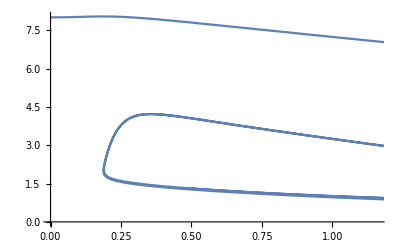

```mathematica
Faz = {};
For[i=1,i≤Length[traektory],i++,Faz = Append[Faz,{traektory⟦i⟧⟦2⟧,traektory⟦i⟧⟦3⟧}]];
ListLinePlot[Faz]
```